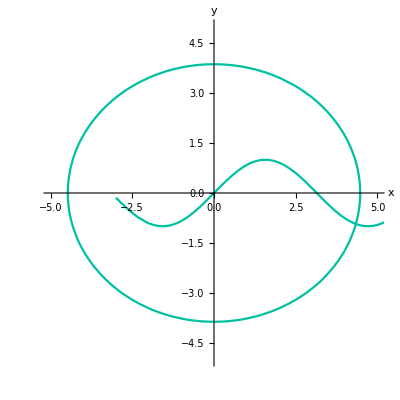

```mathematica
(*函数定义*)plotfun[fun_,xlimits_,ylimits_]:=ContourPlot[fun,xlimits,ylimits,ContourStyle->{RGBColor["#00C0A3"],Thickness[0.004]},AspectRatio->((xlimits[[2]]//Abs)+(xlimits[[3]]//Abs))/((ylimits[[2]]//Abs)+(ylimits[[3]]//Abs)),AxesOrigin->{0,0},Axes->True,Frame->False,AxesStyle->Arrowheads[{0,0.03}],(*0->在正半轴；1->同时在正负半轴*)(*0.03->箭头的大小*)AxesLabel->{"x","y"}]

(*使用方法*)
xlimits={x,-3,6};
ylimits={y,-4,5};
fp31=plotfun[y==Sin[x],xlimits,ylimits];
fp32=plotfun[x^2/4+y^2/3==5,{x,-5,5},{y,-5,5}];

Show[fp32,fp31]
```

```mathematica
Show[%7,Axes->True,AxesStyle->Black]
```

-Graphics-